# Problem Set 2.2

## Ex 1

L21=5

```mathematica
2 x+3 y=1
10 x+9 y=11
({{2, 3}, {0, -6}}).({{x}, {y}})=={1,6}
```

Set::write: Tag Plus in 2 x+3 y is Protected.

1

Set::write: Tag Plus in 10 x+9 y is Protected.

11

{{2 x+3 y},{-6 y}}=={1,6}

## Ex II

```mathematica
Solve[({{2, 0}, {0, -6}}).({{x}, {y}})=={4,6}]
```

{{x→2,y→-1}}

```mathematica
LinearSolve[2*{2,10}+(-1)*{3,9}]
```

LinearSolve::matrix: Argument {1,11} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{1,11}]

```mathematica
Solve[{1,11}]
LinearSolve[8*{2,10}+(-4)*{3,9}]
```

Solve::naqs: 1&&11 is not a quantified system of equations and inequalities.

Solve[{1,11}]

LinearSolve::matrix: Argument {4,44} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{4,44}]

## Ex III

(-1/2)* equation 2

## Ex IV

L=c/a
ax+by=f
(c-ac/a)x+(d-bc/a)y=g+fc/a
(d-bc/a)y=g+fc/a
When ad=bc -> d=bc/a
(d-bc/a)y=(bc/a-bc/a)y=0y

## Ex V

3x + 2y = 10
6x + 4y = Z

```mathematica
Solve[{{3,2},{6,4}}.{{x},{y}}=={10,20}] (*Infinite Solutions*)
```

{{y→5-(3 x)/2}}

[{{3,2},{6,4}}.{{x},{y}}=={10,0}]  (*NO SOLUTION*)

## Ex VI

b=4, g=32

## Ex VII

permanently: a = 2
temporaly = 2(-y+1)/(1-y) ou simply 0
x = (1/4)*(6+18*(a-1)/(2-a))
y=-(a-1)/(2-a)

## Ex VIII

k=-3; infinity solution
k=3; no solution
k=0, 1 solution if we exchange the rows

## Ex IX

b2=2*B1; infinity solutions, for b={1,0} the system has no solution; below there is the row picture for b={1,2}

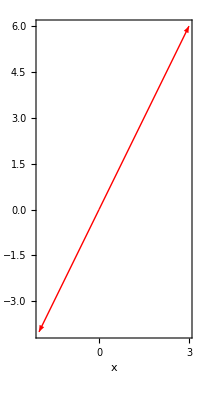

```mathematica
Graphics[{{Red,Arrow[{{0,0},{3,6}}],Arrow[{{0,0},{-2,-4}}]}},Frame->True,FrameLabel->{x,y}]
```

## Ex X

y=1; x=4; c=-9y+25 ou c=y-14/-30

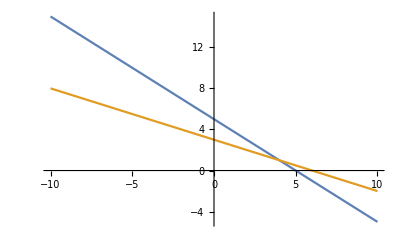

```mathematica
Plot[{5-x,3-x/2},{x,-10,10}]
```

## Ex XI

a) A*(x,y,z)+B*(X,Y.Z) is also a solution, A and B Real numbers.
b) Everywhere if thery are the same plane, or nowhere if they are concurrent.

## Ex XII

```mathematica
({{2, 3, 1}, {0, 1, 3}, {0, 0, 8}}).({{x}, {y}, {z}})={8,4,8}
```

Set::write: Tag Dot in {{2,3,1},{0,1,3},{0,0,8}}.{{x},{y},{z}} is Protected.

{8,4,8}

## Ex XIII

List the three row operations: Subtract 2 times row 1 from row 2
List the three row operations: Subtract 1 time row 1 from row 3 List the three row operations: Subtract 2 times row 2 from row 3

```mathematica
({{2, -3, 3}, {0, 1, 1}, {0, 0, -5}}).({{x}, {y}, {z}})={3,1,0}
```

## Ex XIV

If d=0 we need to do a row exchange. If d=10 the matrix is singular.

```mathematica
({{2, 5, 1}, {4, 0, 1}, {0, 1, -1}}).({{x}, {y}, {z}})={0,1,3}
```

## Ex XV

If b=0 we need to do a row exchange. If b=-1 the matrix is singular. S= {1,1,2}

## Ex XVI

```mathematica
"A)"
```

```mathematica
({{1, 0, 0}, {0, 0, 1}, {0, 1, 1}}).({{x}, {y}, {z}})={0,1,3}
"B)"
({{1, 0, 0}, {0, 0, 1}, {0, 1, 0}}).({{x}, {y}, {z}})={0,1,3}
```

## Ex XVII

You can get to eliminate the third line by subtracting the 3 times the first. The last Pivot is missing,

## Ex XVIII

```mathematica
({{1, 2, 3}, {10, 20, 30}, {100, 200, 300}}).({{x}, {y}, {z}})={1,10,100}
```

The system has infinity solution, bur if I hadn’t chose lines 2 and 3 being igual to 10 and 100 times line 1 the system would have no solution.

## Ex XIX

Singular with no solution: q=-6, t different of 5 ;
Singular with infinitely many solutions : q=-6, t= 5 ;
If z=1: x=-9, y=3, q=t-9.

## Ex XX

Three planes can fail to have an intersection point, even if no planes are parallel. The
system is singular if row 3 of A is a linear combination of the first two rows. Find a third equation
that can’t be solved together with x + y + z = 0 and x - 2y - z = 1.
Since any linear combination is also a solution, so we could choose (x + y + z) + (x - 2y - z) = 1+0 => 2x-y=1

## Ex XXI

```mathematica
({{1, 2, 1, 0}, {0, 1, 2, 1}, {0, 0, 1, 2}, {0, 0, 0, -5}}).({{x}, {y}, {z}, {t}})={0,0,-20,5}
({{1, -2, 1, 0}, {0, 1, -2, 1}, {0, 0, 1, -2}, {0, 0, 0, 9}}).({{x}, {y}, {z}, {t}})={0,0,-5,30}
```

## Ex XXII

The 5th pivot would be 1 and the nth pivoth would be 1 if you extend enough the system.

## Ex XXIII

```mathematica
({{1, 1}, {1, 3}}).({{x}, {y}})={1,4}
({{2, 2}, {1, 3}}).({{x}, {y}})={2,4}
({{2, 2}, {2, 6}}).({{x}, {y}})={2,8}
```

## Ex XXIV

Elimination fais if a=0 and a=2.

## Ex XXV

Elimination fais if a=0, a=4, a=2.

## Ex XXVI

s=10

```mathematica
({{4-b, b}, {b-2, 10-b}})
if b=0
({{4, 0}, {-2, 10}})
({{3, 1}, {-1, 9}})
```

## Ex XXVII

```mathematica
({{3, 0, 0}, {0, 2, 0}, {0, 0, 1}}).({{x}, {y}, {z}})={3,2,2}
S={1,1,2}
```

## Ex XXIX

```mathematica
A=RandomInteger[10,{3,3}]
{lu,p,c}=LUDecomposition[RandomInteger[A]]
```

{{2,3,9},{8,0,7},{1,10,6}}

RandomInteger::parb: {{2,3,9},{8,0,7},{1,10,6}} should have between 0 and 2 parameters.

Set::shape: Lists {lu,p,c} and LUDecomposition[RandomInteger[{{2,3,9},{8,0,7},{1,10,6}}]] are not the same shape.

LUDecomposition[RandomInteger[{{2,3,9},{8,0,7},{1,10,6}}]]

## Ex XXX

If A(5,5)=A(1,5)*A(5,1)/A(1,1) the matriz would be singular, because 0 is different of 1.

## Ex XXXI

Then row j of U is a combination of all (j-1) rows above it. Yes, because any coeficient multiplying 0 is zero, so any combination of 0 subtracted to a row j (also  = 0) is zero, so Ux=0. If Ax=b, it is not necessary that Ux=b because a element of b, b1j, 1<j<=n, is a linear combination of the preceding rows, and if the preceding rows don`t cancel each other and are not null, then Ux is different of b. 
If we diagonilize a lower triangular we end up with a diagonal matriz keeping the same pivots.

## Ex XXXII

a)(a) Elimination takes linear combinations of the rows. So this singular system has
the singular property: Some linear combination of the 100 rows is the 100th row.
(b) Singular systems Ax = 0 have infinitely many solutions. This means that some
linear combination of the 100 columns is 0.
(c) Invent a 100 by 100 singular matrix with no zero entries. ANS: Ny matrix with all Aij=c/xj, Ai(j+1)= -c/xj, c a real number is a solution.
(d) For your matrix, describe in words the row picture and the column picture of
Ax = O. Not necessary to draw 100-dimensional space. A line in 100-dimentional space.

{{4-b,b},{-2+b,10-b}}

```mathematica
LinearSolve[{{-1,1},{0,0}}.{1,1}]
```

LinearSolve::matrix: Argument {0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,0}]

```mathematica
1
LinearSolve[{{-1,1,0},{0,-1,1},{0,0,0}}.{1,1,2}]
```

1

LinearSolve::matrix: Argument {0,1,0} at position 1 is not a non-empty rectangular matrix.

```mathematica
LinearSolve[{0,1,0}]
LinearSolve[{{-1,1,0,0},{0,-1,1,0},{0,0,-1,1},{0,0,0,0}}.{1,1,2,2}]
```

LinearSolve::matrix: Argument {0,1,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0}]

LinearSolve::matrix: Argument {0,1,0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,0}]

```mathematica
LinearSolve[{{-1,1,0,0,0},{0,-1,1,0,0},{0,0,-1,1,0},{0,0,0,-1,1},{0,0,0,0,0}}.{1,1,2,2,4}]
LinearSolve[{{-1,1,0,0,0,0},{0,-1,1,0,0,0},{0,0,-1,1,0,0},{0,0,0,-1,1,0},{0,0,0,0,-1,1},{0,0,0,0,0,0}}.{1,1,2,2,4,2}]
LinearSolve[{{-1,1,0,0,0,0,0},{0,-1,1,0,0,0,0},{0,0,-1,1,0,0,0},{0,0,0,-1,1,0,0},{0,0,0,0,-1,1,0},{0,0,0,0,0,-1,1},{0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6}]
LinearSolve[{{-1,1,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0},{0,0,-1,1,0,0,0,0},{0,0,0,-1,1,0,0,0},{0,0,0,0,-1,1,0,0},{0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4}]
LinearSolve[{{-1,1,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0},{0,0,-1,1,0,0,0,0},{0,0,0,-1,1,0,0,0},{0,0,0,0,-1,1,0,0},{0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0},{0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8,16}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8,16,6}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8,16,6,18}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8,16,6,18,8}]
LinearSolve[{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,1,2,2,4,2,6,4,6,4,10,4,12,6,8,8,16,6,18,8,12}]
```

LinearSolve::matrix: Argument {0,1,0,2,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,12,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,12,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,12,-10,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,12,-10,0}]

LinearSolve::matrix: Argument {0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,12,-10,4,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,1,0,2,-2,4,-2,2,-2,6,-6,8,-6,2,0,8,-10,12,-10,4,0}]